The zero crossing of F is z1=0.208367

The zero crossing of F is z1=1.12427

The steady state of the SSN is re=0.0434166, ri=1.41978

The steady state of the SSN is re=1.26399, ri=2.70091

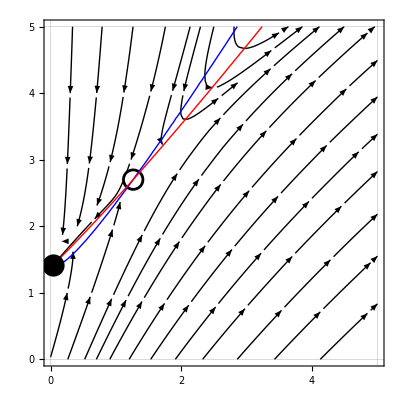

```mathematica
taue = 0.020;
taui = 0.010;
Jee = 1.8;
Jei = 1.0;
Jie = 1.0;
Jii = 0.6;
nE = 2;
nI = 2;
ge =1.55;
gi = 2;

cplus = - Jei^(-1)*Jii*ge + gi;
cminus = - Jie^(-1)*Jee*gi + ge;
detJ = -Jee*Jii + Jei*Jie;

P[z_] = detJ * Jei^(-1)*Piecewise[{{z^nE, z>0}, {0, z≤0}}]+Jei^(-1)*Jii*z + cplus;
F[z_] = Jee*Piecewise[{{z^nE, z>0}, {0, z≤0}}] - Jei*Piecewise[{{(P[z])^nI, P[z]>0}, {0, P[z]≤0}}]-z+ge;

z0 =Solve[P[z] ==0, z];
Z = Solve[F[z]==0, z];
Print["The zero crossing of F is z1=", z/.Z[[1]]]
Print["The zero crossing of F is z1=", z/.Z[[2]]]

re1 = ((z/.Z[[1]]) * HeavisideTheta[(z/.Z[[1]])])^nE;
ri1 = ((detJ*Jei^(-1)* (z/.Z[[1]])^nE+ Jei^(-1) *Jii*(z/.Z[[1]]) + cplus)* HeavisideTheta[(detJ*Jei^(-1)* (z/.Z[[1]])^nE+ Jei^(-1) *Jii*(z/.Z[[1]]) + cplus)])^nI;
Print["The steady state of the SSN is re=", re1, ", ri=", ri1];

re2 = ((z/.Z[[2]]) * HeavisideTheta[(z/.Z[[2]])])^nE;
ri2 = ((detJ*Jei^(-1)* (z/.Z[[2]])^nE+ Jei^(-1) *Jii*(z/.Z[[2]]) + cplus)* HeavisideTheta[(detJ*Jei^(-1)* (z/.Z[[2]])^nE+ Jei^(-1) *Jii*(z/.Z[[2]]) + cplus)])^nI;
Print["The steady state of the SSN is re=", re2, ", ri=", ri2];

Ge[x_, y_] :=(-x+(Jee*x-Jei*y+ge)^nE*HeavisideTheta[Jee*x-Jei*y+ge])*(taue)^(-1);Gi[x_, y_] :=(-y+(Jie*x-Jii*y+gi)^nI*HeavisideTheta[Jie*x-Jii*y+gi])*(taui)^(-1);

cp=ContourPlot[{Ge[x,y]==0,Gi[x,y]==0},{x,0,5},{y,0,5}, ContourStyle->{Directive[Thick, Blue], Directive[Thick, Red]}];

splot=StreamPlot[{Ge[x,y],Gi[x,y]},{x,0,5},{y,0,5},StreamColorFunction->None, StreamStyle->Black,StreamScale->0.2,StreamPoints->20,Epilog->{PointSize[0.04],Point[{{re1, ri1}},VertexColors->{Black}]},GridLines->{{{0,Gray},{5,Gray}},{{0,Gray},{5,Gray}}},FrameTicks->{{{0, 1, 2, 3, 4, 5}, None}, {{0, 1, 2, 3, 4, 5}, None}}];
unstable=Graphics[{{PointSize[0.04],Point[ {re2, ri2}]},White,PointSize[0.03],Point[ {re2, ri2}]}];
weakinputwithoutSTP = Show[splot, unstable, cp]
Export[NotebookDirectory[]<>"Fig_2_Supralinear_network_2D_before_stimulation.pdf",weakinputwithoutSTP,"AllowRasterization"->False];
```